```mathematica
NS[]
```

```mathematica
Co[x_]:=Flatten[{1-Total[Flatten[{x}]],x}];
```

```mathematica
SVL=SingularValueList;
```

```mathematica
nn=2;n=1;
u=Table[1,n+1];
uu=Table[1,nn+1];
```

```mathematica
(hh=Table[Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa],{a,0,n},{aa,0,nn}])//MF
```

(1 | 1/2 | 0
0 | 1/2 | 1)

```mathematica
rep=FS[RotationMatrix[{{1,1},{Cos[Pi/6],Sin[Pi/6]}}].{{1,0,0},{0,1,0}}.RotationMatrix[{{1,1,1},{0,0,1}}]];
```

```mathematica
simp=Graphics[{Line[{rep.{1,0,0},rep.{0,1,0},rep.{0,0,1},rep.{1,0,0}}]}];
```

```mathematica
fi={3/5};f0=Co[fi];
```

```mathematica
ffi={ff1,ff2};ffx=Co[ffi];
```

```mathematica
sol=Solve[hh.ffx==f0,ffi]
```

{{ff2→3/5-ff1/2}}

```mathematica
ker=Co[{ff1,ff2/.sol}];
```

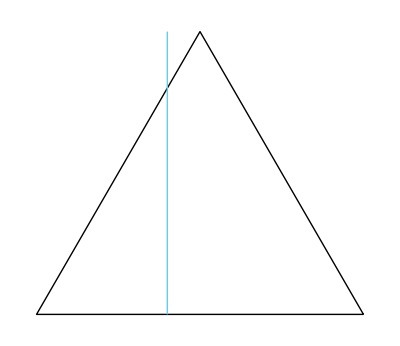

```mathematica
Show[{simp,kerplot=ListPlot[FS@T[rep.T@Table[ker,{ff1,0,1,0.1}]],Joined->True,AspectRatio->1]}]
```

```mathematica
(MF@SVL[T[hh].hh+#,3]//N)&/@{0,-10,10,Abs[eps]}
```

{(1.5
1.
0.),(28.5
1.
0.),(31.5
1.
0.),(1.
1.5 √(1.+4. Abs[eps]+4. Abs[eps]^2)
0.)}

```mathematica
(* the cov matrix obtained from the projection matrix IS in standard form! *)
```

```mathematica
hhf=hh-T[{f0}].{uu};
```

```mathematica
Assuming[eps>0,FS[(MF@SVL[T[hhf].hhf+#,3]//N)&/@{0,-10,10,eps}]]
```

{(1.06
0.
0.),(29.9419
1.00194
0.),(30.0621
0.997935
0.),(0.0141421 √(2809.+900. eps+22500. eps^2+√(-2.25×10^8 eps^2+(2809.+eps (900.+22500. eps))^2))
0.0141421 √(2809.+900. eps+22500. eps^2-22500. (0.353333+1. eps) √(0.124844+eps (-0.626667+1. eps)))
0.)}

```mathematica
(* the cov matrix obtained from projection matrix - target freq is NOT in standard form! *)
```

```mathematica
ffs=PseudoInverse[hh].f0
```

{7/30,1/3,13/30}

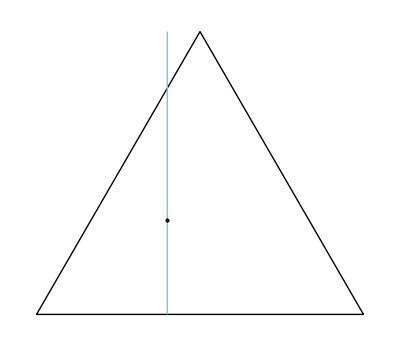

```mathematica
Show[{simp,kerplot,Graphics[Point[rep.ffs]]}]
```

```mathematica
rm2=RotationMatrix[{{1,1},{0,1}}];
```

```mathematica
fx=Co[f1];
```

```mathematica
$Assumptions = (eps>0);
```

```mathematica
cm0=FS[T[rm2].{{1/(1/10)^2,0},{0,eps}}.rm2]
```

{{50+eps/2,-50+eps/2},{-50+eps/2,50+eps/2}}

```mathematica
FS@SVL[cm0,2]
```

{100,eps}

```mathematica
FS[(fx-f0).(cm0).(fx-f0)]
```

8 (3-5 f1)^2

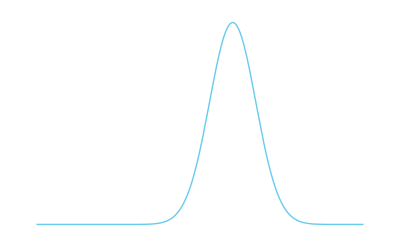

```mathematica
Plot[Evaluate@Exp[-1/2*FS[(fx-f0).(cm0).(fx-f0)]],{f1,0,1}]
```

```mathematica
FS[(MF@SVL[(sig=T[hh].(cm0/.(eps->0)).hh)+#,3]//N)&/@{0,-10,10,Abs[eps]}]
```

{(100.
0.
0.),(100.
30.
0.),(100.
30.
0.),(100.
3. eps
0.)}

```mathematica
FS[T[hh].((cm0/.(eps->0))+eps).hh-eps]//MF
```

(50 | 0 | -50
0 | 0 | 0
-50 | 0 | 50)

```mathematica
FS[T[hh].((cm0/.(eps->0))).hh]//MF
```

(50 | 0 | -50
0 | 0 | 0
-50 | 0 | 50)

```mathematica
(* the cov matrix obtained from the projection matrix seems to be in standard form! *)
```

```mathematica
sol2=Solve[(ffx-ffs).sig.(ffx-ffs)==1,ffi]
```

{{ff2→1/20 (12-√2-10 ff1)},{ff2→1/20 (12+√2-10 ff1)}}

```mathematica
ker2=Co[{ff1,ff2/.sol2[[2]]}];
```

```mathematica
sol3=Solve[(f0-hh.ffx).cm0.(f0-hh.ffx)==1,ffi]
```

{{ff2→1/20 (12-√2-10 ff1)},{ff2→1/20 (12+√2-10 ff1)}}

```mathematica
ker3=Co[{ff1,ff2/.sol3[[2]]}];
```

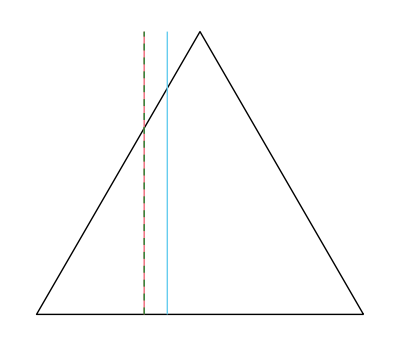

```mathematica
Show[{simp,kerplot,kerplot2=ListPlot[FS@T[rep.T@Table[ker2,{ff1,0,1,0.1}]],Joined->True,AspectRatio->1,PlotStyle->{Thick,red}],kerplot3=ListPlot[FS@T[rep.T@Table[ker3,{ff1,0,1,0.1}]],Joined->True,AspectRatio->1,PlotStyle->{Dashed,green}]}]
```

```mathematica
cm0d=FS[rm2.cm0.T[rm2]]
```

{{100,0},{0,eps}}

```mathematica
rm3=FS@RotationMatrix[{{1,1,1},{0,0,1}}];
```

```mathematica
FS@SVL[sig+eps,3]
```

{100,3 eps,0}

```mathematica
MF@FS[rm3.sig.T[rm3]]
```

(25 (2+√3) | 25 | 0
25 | -25 (-2+√3) | 0
0 | 0 | 0)

```mathematica
MF[sigr=FS[rm3.(sig).T[rm3]]]
```

(25 (2+√3) | 25 | 0
25 | -25 (-2+√3) | 0
0 | 0 | 0)

```mathematica
MF@FS[rm3.(sig+eps).T[rm3]]
```

(25 (2+√3) | 25 | 0
25 | -25 (-2+√3) | 0
0 | 0 | 3 eps)

```mathematica
FS[(MF@SVL[sigr+DiagonalMatrix[{0,0,eps}],3]//N)&/@{0,-10,10,Abs[eps]}]
```

{(100.
eps
0.),(100.
eps
0.),(100.
eps
0.),(100.
eps
0.)}

```mathematica
(* Let's try with the specific matrices of our problem *)
```

```mathematica
t=15;tt=50;n=65;nnn=1000;
hhh=Table[Binomial[t,a]*Binomial[nnn-t,aa-a]/Binomial[nnn,aa],{a,0,t},{aa,0,tt}];
ut=Table[1,{t+1}];utt=Table[1,{tt+1}];
```

```mathematica
le=417641;freqs=Round[Flatten@Import["_scripts-mc_fullnetwork\\stensola_activity_freqs_bins417641.csv"]*le]/le;
n=Length[freqs]-1;
```

```mathematica
gfc=Import["_scripts-mc_fullnetwork\\stensola_devc10000_fcov.csv"][[;;t+1,;;t+1]];
```

```mathematica
printnumber[SVL[gfc,t+1],2]
```

{9.2e-7,2.9e-8,1.1e-8,3.5e-9,9.5e-10,2.5e-10,5.5e-11,1.2e-11,1.8e-12,1.1e-13,0,0,0,0,0,0}

```mathematica
printnumber[SVL[gfc+100,t+1],2]
```

{1.6e3,9.2e-7,2.9e-8,1.1e-8,3.5e-9,9.5e-10,2.5e-10,5.5e-11,0,0,0,0,0,0,0,0}

```mathematica
printnumber[Eigenvalues[gfc,t+1],2]
```

{9.2e-7,2.9e-8,1.1e-8,3.5e-9,9.5e-10,2.5e-10,5.5e-11,1.2e-11,1.8e-12,1.1e-13,-7.9e-23,0,0,0,0,0}

```mathematica
printnumber[Eigenvalues[gfc+10^-7,t+1],2]
```

{1.6e-6,9.2e-7,2.9e-8,1.1e-8,3.5e-9,9.5e-10,2.5e-10,5.5e-11,1.2e-11,1.8e-12,1.1e-13,-2.8e-22,-7.e-23,3.2e-23,-7.1e-24,6.9e-24}

```mathematica
rmt=FS[RotationMatrix[{ut,PadRight[{1},t+1]}]];
```

```mathematica
MF[(printnumber[Eigenvalues[rmt.gfc.T[rmt]+PadRight[{#},t+1],t+1],2])&/@{0,-100,100}]
```

(9.2e-7 | 2.9e-8 | 1.1e-8 | 3.5e-9 | 9.5e-10 | 2.5e-10 | 5.5e-11 | 1.2e-11 | 1.8e-12 | 1.1e-13 | -2.e-22 | -8.6e-24 | 7.3e-25 | 1.4e-27 | -8.6e-37 | 5.3e-37 | 5.3e-37 | -4.1e-37 | -2.5e-37 | -2.5e-37 | -1.8e-37 | 1.6e-37 | 1.6e-37 | 1.6e-37 | 1.1e-37 | 1.1e-37 | -7.7e-38 | -6.9e-38 | -6.9e-38 | 6.6e-38 | 5.9e-38 | 5.9e-38 | -5.5e-38 | -5.5e-38 | 9.e-39 | 4.7e-40 | -6.8e-55 | 3.e-55 | 3.e-55 | 1.8e-55 | 1.8e-55 | 1.7e-55 | 1.4e-55 | 1.4e-55 | -1.3e-55 | 1.2e-55 | 1.2e-55 | -3.5e-56 | -3.2e-56 | 2.4e-56 | 2.4e-56 | -2.e-56 | 9.4e-57 | -4.9e-57 | -4.9e-57 | -9.4e-58 | -9.4e-58 | 5.5e-58 | 5.5e-58 | 2.e-58 | -1.5e-58 | -1.5e-58 | -7.5e-59 | 9.6e-60 | -2.2e-60 | -9.3e-62
-1.e2 | 9.2e-7 | 2.9e-8 | 1.1e-8 | 3.5e-9 | 9.5e-10 | 2.5e-10 | 5.5e-11 | 1.2e-11 | 1.8e-12 | 1.1e-13 | -2.4e-22 | 8.6e-25 | 6.7e-28 | -8.6e-37 | 5.3e-37 | 5.3e-37 | -4.1e-37 | -2.5e-37 | -2.5e-37 | -1.8e-37 | 1.6e-37 | 1.6e-37 | 1.6e-37 | 1.1e-37 | 1.1e-37 | -7.7e-38 | -6.9e-38 | -6.9e-38 | 6.6e-38 | 5.9e-38 | 5.9e-38 | -5.5e-38 | -5.5e-38 | 9.e-39 | 4.7e-40 | -6.8e-55 | 3.e-55 | 3.e-55 | 1.8e-55 | 1.8e-55 | 1.7e-55 | 1.4e-55 | 1.4e-55 | -1.3e-55 | 1.2e-55 | 1.2e-55 | -3.5e-56 | -3.2e-56 | 2.4e-56 | 2.4e-56 | -2.e-56 | 9.4e-57 | -4.9e-57 | -4.9e-57 | -9.4e-58 | -9.4e-58 | 5.5e-58 | 5.5e-58 | 2.e-58 | -1.5e-58 | -1.5e-58 | -7.5e-59 | 9.6e-60 | -2.2e-60 | -9.3e-62
1.e2 | 9.2e-7 | 2.9e-8 | 1.1e-8 | 3.5e-9 | 9.5e-10 | 2.5e-10 | 5.5e-11 | 1.2e-11 | 1.8e-12 | 1.1e-13 | -2.4e-22 | 8.6e-25 | 6.8e-28 | -8.6e-37 | 5.3e-37 | 5.3e-37 | -4.1e-37 | -2.5e-37 | -2.5e-37 | -1.8e-37 | 1.6e-37 | 1.6e-37 | 1.6e-37 | 1.1e-37 | 1.1e-37 | -7.7e-38 | -6.9e-38 | -6.9e-38 | 6.6e-38 | 5.9e-38 | 5.9e-38 | -5.5e-38 | -5.5e-38 | 9.e-39 | 4.7e-40 | -6.8e-55 | 3.e-55 | 3.e-55 | 1.8e-55 | 1.8e-55 | 1.7e-55 | 1.4e-55 | 1.4e-55 | -1.3e-55 | 1.2e-55 | 1.2e-55 | -3.5e-56 | -3.2e-56 | 2.4e-56 | 2.4e-56 | -2.e-56 | 9.4e-57 | -4.9e-57 | -4.9e-57 | -9.4e-58 | -9.4e-58 | 5.5e-58 | 5.5e-58 | 2.e-58 | -1.5e-58 | -1.5e-58 | -7.5e-59 | 9.6e-60 | -2.2e-60 | -9.3e-62)

```mathematica
svg=SVD[gfc,t+1,Tolerance->1/(4*le)^2];
```

```mathematica
vart=Diagonal[svg[[2]]]
```

{9.19214×10^-7,2.91878×10^-8,1.12554×10^-8,3.50454×10^-9,9.5114×10^-10,2.45421×10^-10,5.47838×10^-11,1.15516×10^-11,1.81341×10^-12,1.0696×10^-13,0.,0.,0.,0.,0.,0.}

```mathematica
newvart=vart+1/(le/2)^2
```

{9.19237×10^-7,2.92108×10^-8,1.12784×10^-8,3.52747×10^-9,9.74072×10^-10,2.68354×10^-10,7.77164×10^-11,3.44843×10^-11,2.4746×10^-11,2.30396×10^-11,2.29326×10^-11,2.29326×10^-11,2.29326×10^-11,2.29326×10^-11,2.29326×10^-11,2.29326×10^-11}

```mathematica
inewgfchalf=DiagonalMatrix[1/Sqrt[newvart]].T[svg[[3]]];
```

```mathematica
mm=inewgfchalf.hhh;
```

```mathematica
{Min@Abs@Flatten[#],Max@Abs@Flatten[#]}&@mm
```

{0.,62961.7}

```mathematica
printnumber[mm,3]//MF
```

(-926. | -908. | -890. | -872. | -855. | -838. | -821. | -804. | -787. | -771. | -755. | -739. | -723. | -708. | -693. | -678. | -663. | -648. | -634. | -620. | -606. | -592. | -579. | -565. | -552. | -539. | -526. | -514. | -501. | -489. | -477. | -465. | -453. | -442. | -431. | -419. | -408. | -398. | -387. | -376. | -366. | -356. | -346. | -336. | -326. | -316. | -307. | -298. | -289. | -280. | -271.
-25.2 | -92.1 | -156. | -218. | -277. | -334. | -388. | -440. | -489. | -536. | -582. | -625. | -666. | -705. | -742. | -777. | -810. | -842. | -872. | -900. | -926. | -951. | -975. | -996. | -1.02e3 | -1.04e3 | -1.05e3 | -1.07e3 | -1.08e3 | -1.1e3 | -1.11e3 | -1.12e3 | -1.13e3 | -1.14e3 | -1.15e3 | -1.16e3 | -1.16e3 | -1.17e3 | -1.17e3 | -1.17e3 | -1.18e3 | -1.18e3 | -1.18e3 | -1.18e3 | -1.18e3 | -1.17e3 | -1.17e3 | -1.17e3 | -1.16e3 | -1.16e3 | -1.15e3
-876. | -910. | -944. | -978. | -1.01e3 | -1.04e3 | -1.08e3 | -1.11e3 | -1.14e3 | -1.17e3 | -1.2e3 | -1.23e3 | -1.26e3 | -1.29e3 | -1.32e3 | -1.35e3 | -1.37e3 | -1.4e3 | -1.43e3 | -1.45e3 | -1.48e3 | -1.5e3 | -1.53e3 | -1.55e3 | -1.57e3 | -1.59e3 | -1.61e3 | -1.63e3 | -1.65e3 | -1.67e3 | -1.69e3 | -1.7e3 | -1.72e3 | -1.74e3 | -1.75e3 | -1.77e3 | -1.78e3 | -1.79e3 | -1.8e3 | -1.82e3 | -1.83e3 | -1.84e3 | -1.85e3 | -1.85e3 | -1.86e3 | -1.87e3 | -1.87e3 | -1.88e3 | -1.89e3 | -1.89e3 | -1.89e3
-2.04e3 | -2.05e3 | -2.06e3 | -2.08e3 | -2.09e3 | -2.11e3 | -2.12e3 | -2.14e3 | -2.16e3 | -2.17e3 | -2.19e3 | -2.2e3 | -2.22e3 | -2.24e3 | -2.25e3 | -2.27e3 | -2.28e3 | -2.3e3 | -2.32e3 | -2.33e3 | -2.35e3 | -2.37e3 | -2.38e3 | -2.4e3 | -2.41e3 | -2.43e3 | -2.45e3 | -2.46e3 | -2.48e3 | -2.49e3 | -2.51e3 | -2.52e3 | -2.54e3 | -2.55e3 | -2.57e3 | -2.58e3 | -2.59e3 | -2.61e3 | -2.62e3 | -2.64e3 | -2.65e3 | -2.66e3 | -2.67e3 | -2.68e3 | -2.7e3 | -2.71e3 | -2.72e3 | -2.73e3 | -2.74e3 | -2.75e3 | -2.76e3
-4.32e3 | -4.33e3 | -4.34e3 | -4.34e3 | -4.35e3 | -4.36e3 | -4.37e3 | -4.37e3 | -4.38e3 | -4.39e3 | -4.4e3 | -4.41e3 | -4.42e3 | -4.43e3 | -4.44e3 | -4.45e3 | -4.46e3 | -4.47e3 | -4.48e3 | -4.49e3 | -4.5e3 | -4.51e3 | -4.52e3 | -4.53e3 | -4.54e3 | -4.55e3 | -4.56e3 | -4.57e3 | -4.58e3 | -4.59e3 | -4.6e3 | -4.61e3 | -4.63e3 | -4.64e3 | -4.65e3 | -4.66e3 | -4.67e3 | -4.68e3 | -4.69e3 | -4.7e3 | -4.71e3 | -4.72e3 | -4.74e3 | -4.75e3 | -4.76e3 | -4.77e3 | -4.78e3 | -4.79e3 | -4.8e3 | -4.81e3 | -4.82e3
-8.37e3 | -8.37e3 | -8.37e3 | -8.38e3 | -8.38e3 | -8.38e3 | -8.39e3 | -8.39e3 | -8.4e3 | -8.4e3 | -8.4e3 | -8.41e3 | -8.41e3 | -8.42e3 | -8.42e3 | -8.43e3 | -8.44e3 | -8.44e3 | -8.45e3 | -8.45e3 | -8.46e3 | -8.47e3 | -8.47e3 | -8.48e3 | -8.48e3 | -8.49e3 | -8.5e3 | -8.51e3 | -8.51e3 | -8.52e3 | -8.53e3 | -8.53e3 | -8.54e3 | -8.55e3 | -8.56e3 | -8.56e3 | -8.57e3 | -8.58e3 | -8.59e3 | -8.6e3 | -8.6e3 | -8.61e3 | -8.62e3 | -8.63e3 | -8.64e3 | -8.64e3 | -8.65e3 | -8.66e3 | -8.67e3 | -8.68e3 | -8.69e3
-1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.51e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.52e4 | -1.53e4 | -1.53e4 | -1.53e4 | -1.53e4 | -1.53e4 | -1.53e4
-2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.19e4 | -2.2e4 | -2.2e4 | -2.2e4 | -2.2e4 | -2.2e4
-2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4 | -2.47e4
-2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4 | -2.13e4
6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4 | 6.3e4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.03e-28 | 4.86e-27 | 4.13e-26 | 2.48e-25 | 1.18e-24 | 4.7e-24 | 1.65e-23 | 5.18e-23 | 1.49e-22 | 3.97e-22 | 9.92e-22 | 2.34e-21 | 5.28e-21 | 1.14e-20 | 2.35e-20 | 4.71e-20 | 9.12e-20 | 1.72e-19 | 3.15e-19 | 5.63e-19 | 9.86e-19 | 1.69e-18 | 2.84e-18 | 4.69e-18 | 7.63e-18 | 1.22e-17 | 1.92e-17 | 2.99e-17 | 4.6e-17 | 6.98e-17 | 1.05e-16 | 1.55e-16 | 2.28e-16 | 3.32e-16 | 4.78e-16 | 6.83e-16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.99e-25 | 4.48e-24 | 3.58e-23 | 2.03e-22 | 9.12e-22 | 3.46e-21 | 1.15e-20 | 3.45e-20 | 9.49e-20 | 2.42e-19 | 5.81e-19 | 1.32e-18 | 2.85e-18 | 5.92e-18 | 1.18e-17 | 2.29e-17 | 4.28e-17 | 7.8e-17 | 1.38e-16 | 2.4e-16 | 4.08e-16 | 6.79e-16 | 1.11e-15 | 1.78e-15 | 2.82e-15 | 4.4e-15 | 6.76e-15 | 1.03e-14 | 1.54e-14 | 2.28e-14 | 3.33e-14 | 4.84e-14 | 6.94e-14 | 9.88e-14 | 1.39e-13 | 1.95e-13 | 2.7e-13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.48e-22 | 2.06e-21 | 1.54e-20 | 8.22e-20 | 3.49e-19 | 1.25e-18 | 3.96e-18 | 1.13e-17 | 2.96e-17 | 7.21e-17 | 1.66e-16 | 3.6e-16 | 7.49e-16 | 1.5e-15 | 2.88e-15 | 5.36e-15 | 9.7e-15 | 1.71e-14 | 2.94e-14 | 4.93e-14 | 8.12e-14 | 1.31e-13 | 2.08e-13 | 3.25e-13 | 5.01e-13 | 7.6e-13 | 1.14e-12 | 1.68e-12 | 2.46e-12 | 3.55e-12 | 5.08e-12 | 7.19e-12 | 1.01e-11 | 1.4e-11 | 1.94e-11 | 2.65e-11 | 3.6e-11 | 4.85e-11
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.86e-20 | 6.3e-19 | 4.4e-18 | 2.19e-17 | 8.74e-17 | 2.96e-16 | 8.86e-16 | 2.4e-15 | 5.98e-15 | 1.39e-14 | 3.05e-14 | 6.36e-14 | 1.27e-13 | 2.43e-13 | 4.5e-13 | 8.07e-13 | 1.41e-12 | 2.4e-12 | 3.98e-12 | 6.47e-12 | 1.03e-11 | 1.62e-11 | 2.49e-11 | 3.78e-11 | 5.65e-11 | 8.34e-11 | 1.22e-10 | 1.75e-10 | 2.49e-10 | 3.51e-10 | 4.9e-10 | 6.78e-10 | 9.29e-10 | 1.26e-9 | 1.7e-9 | 2.28e-9 | 3.03e-9 | 4.e-9 | 5.25e-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2e-17 | 1.44e-16 | 9.3e-16 | 4.32e-15 | 1.61e-14 | 5.15e-14 | 1.45e-13 | 3.72e-13 | 8.8e-13 | 1.95e-12 | 4.07e-12 | 8.11e-12 | 1.55e-11 | 2.85e-11 | 5.06e-11 | 8.74e-11 | 1.47e-10 | 2.41e-10 | 3.86e-10 | 6.08e-10 | 9.38e-10 | 1.42e-9 | 2.13e-9 | 3.13e-9 | 4.55e-9 | 6.52e-9 | 9.24e-9 | 1.29e-8 | 1.8e-8 | 2.47e-8 | 3.36e-8 | 4.53e-8 | 6.06e-8 | 8.05e-8 | 1.06e-7 | 1.39e-7 | 1.81e-7 | 2.33e-7 | 2.99e-7 | 3.82e-7)

```mathematica
finmm=inewgfchalf.(hhh-T[{freqs[[;;t+1]]}].{utt});
```

```mathematica
printnumber[finmm,3]//MF
```

(-605. | -587. | -569. | -551. | -534. | -517. | -500. | -483. | -466. | -450. | -434. | -418. | -402. | -387. | -372. | -357. | -342. | -327. | -313. | -299. | -285. | -271. | -258. | -244. | -231. | -218. | -205. | -193. | -180. | -168. | -156. | -144. | -132. | -121. | -109. | -98.3 | -87.3 | -76.4 | -65.7 | -55.2 | -44.8 | -34.6 | -24.6 | -14.7 | -4.94 | 4.65 | 14.1 | 23.4 | 32.5 | 41.5 | 50.4
850. | 783. | 719. | 657. | 598. | 542. | 487. | 436. | 386. | 339. | 293. | 250. | 209. | 170. | 133. | 98.1 | 64.7 | 33.2 | 3.33 | -24.8 | -51.3 | -76.2 | -99.5 | -121. | -142. | -161. | -178. | -194. | -209. | -223. | -236. | -247. | -257. | -266. | -274. | -281. | -287. | -291. | -295. | -298. | -301. | -302. | -302. | -302. | -301. | -299. | -297. | -293. | -289. | -285. | -280.
655. | 621. | 587. | 553. | 520. | 487. | 455. | 423. | 391. | 360. | 329. | 299. | 270. | 241. | 212. | 184. | 157. | 130. | 104. | 78.6 | 53.8 | 29.7 | 6.25 | -16.5 | -38.6 | -60. | -80.7 | -101. | -120. | -139. | -156. | -174. | -190. | -206. | -221. | -235. | -248. | -261. | -273. | -284. | -295. | -305. | -314. | -322. | -330. | -337. | -343. | -349. | -354. | -358. | -362.
453. | 439. | 424. | 410. | 395. | 380. | 364. | 349. | 333. | 318. | 302. | 286. | 270. | 253. | 237. | 221. | 205. | 188. | 172. | 156. | 139. | 123. | 107. | 91. | 74.9 | 59. | 43.2 | 27.5 | 11.9 | -3.46 | -18.7 | -33.7 | -48.6 | -63.2 | -77.7 | -91.9 | -106. | -120. | -133. | -146. | -159. | -171. | -184. | -196. | -207. | -218. | -229. | -240. | -250. | -260. | -269.
334. | 327. | 320. | 313. | 305. | 298. | 290. | 281. | 273. | 264. | 256. | 247. | 238. | 228. | 219. | 209. | 200. | 190. | 180. | 170. | 160. | 149. | 139. | 128. | 118. | 107. | 96.2 | 85.3 | 74.4 | 63.4 | 52.4 | 41.3 | 30.3 | 19.1 | 8.03 | -3.09 | -14.2 | -25.3 | -36.4 | -47.4 | -58.4 | -69.3 | -80.2 | -91. | -102. | -112. | -123. | -133. | -144. | -154. | -164.
236. | 233. | 230. | 226. | 223. | 219. | 215. | 211. | 207. | 202. | 198. | 193. | 188. | 183. | 178. | 172. | 167. | 161. | 155. | 150. | 143. | 137. | 131. | 124. | 118. | 111. | 104. | 97.2 | 90.2 | 83. | 75.7 | 68.4 | 60.9 | 53.4 | 45.7 | 38. | 30.3 | 22.4 | 14.5 | 6.55 | -1.46 | -9.53 | -17.6 | -25.8 | -33.9 | -42.1 | -50.3 | -58.6 | -66.8 | -75. | -83.2
134. | 133. | 132. | 130. | 129. | 127. | 126. | 124. | 122. | 120. | 118. | 116. | 114. | 111. | 109. | 106. | 104. | 101. | 98. | 95.1 | 92. | 88.9 | 85.7 | 82.4 | 79. | 75.5 | 72. | 68.3 | 64.6 | 60.8 | 56.9 | 53. | 48.9 | 44.9 | 40.7 | 36.5 | 32.2 | 27.8 | 23.4 | 18.9 | 14.4 | 9.76 | 5.12 | 0.424 | -4.32 | -9.1 | -13.9 | -18.8 | -23.7 | -28.6 | -33.6
60.9 | 60.5 | 60.1 | 59.6 | 59.1 | 58.6 | 58. | 57.4 | 56.7 | 56. | 55.3 | 54.5 | 53.6 | 52.7 | 51.8 | 50.8 | 49.8 | 48.8 | 47.7 | 46.5 | 45.4 | 44.1 | 42.9 | 41.6 | 40.2 | 38.9 | 37.4 | 36. | 34.5 | 32.9 | 31.4 | 29.7 | 28.1 | 26.4 | 24.7 | 22.9 | 21.1 | 19.3 | 17.4 | 15.5 | 13.6 | 11.6 | 9.65 | 7.63 | 5.57 | 3.49 | 1.38 | -0.753 | -2.92 | -5.1 | -7.32
19.3 | 19.1 | 19. | 18.8 | 18.6 | 18.4 | 18.2 | 18. | 17.8 | 17.5 | 17.3 | 17. | 16.7 | 16.4 | 16.1 | 15.8 | 15.5 | 15.1 | 14.8 | 14.4 | 14. | 13.6 | 13.2 | 12.8 | 12.3 | 11.9 | 11.4 | 11. | 10.5 | 10. | 9.51 | 9. | 8.48 | 7.95 | 7.41 | 6.86 | 6.31 | 5.74 | 5.16 | 4.58 | 3.99 | 3.38 | 2.78 | 2.16 | 1.54 | 0.904 | 0.266 | -0.378 | -1.03 | -1.69 | -2.35
0.796 | 0.852 | 0.904 | 0.952 | 0.996 | 1.04 | 1.07 | 1.11 | 1.14 | 1.17 | 1.19 | 1.21 | 1.23 | 1.25 | 1.26 | 1.27 | 1.27 | 1.28 | 1.28 | 1.28 | 1.27 | 1.26 | 1.25 | 1.24 | 1.23 | 1.21 | 1.19 | 1.17 | 1.15 | 1.12 | 1.1 | 1.07 | 1.03 | 1. | 0.966 | 0.93 | 0.891 | 0.851 | 0.81 | 0.766 | 0.722 | 0.675 | 0.628 | 0.579 | 0.529 | 0.477 | 0.425 | 0.371 | 0.316 | 0.26 | 0.204
-1.44e-9 | -1.43e-9 | -1.42e-9 | -1.4e-9 | -1.38e-9 | -1.36e-9 | -1.35e-9 | -1.32e-9 | -1.3e-9 | -1.28e-9 | -1.26e-9 | -1.23e-9 | -1.21e-9 | -1.18e-9 | -1.16e-9 | -1.12e-9 | -1.09e-9 | -1.06e-9 | -1.03e-9 | -1.e-9 | -9.73e-10 | -9.39e-10 | -9.03e-10 | -8.74e-10 | -8.43e-10 | -8.12e-10 | -7.86e-10 | -7.67e-10 | -7.57e-10 | -7.64e-10 | -7.91e-10 | -8.51e-10 | -9.56e-10 | -1.13e-9 | -1.39e-9 | -1.78e-9 | -2.34e-9 | -3.12e-9 | -4.21e-9 | -5.7e-9 | -7.7e-9 | -1.04e-8 | -1.39e-8 | -1.85e-8 | -2.46e-8 | -3.23e-8 | -4.23e-8 | -5.5e-8 | -7.1e-8 | -9.13e-8 | -1.17e-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.03e-28 | 4.86e-27 | 4.13e-26 | 2.48e-25 | 1.18e-24 | 4.7e-24 | 1.65e-23 | 5.18e-23 | 1.49e-22 | 3.97e-22 | 9.92e-22 | 2.34e-21 | 5.28e-21 | 1.14e-20 | 2.35e-20 | 4.71e-20 | 9.12e-20 | 1.72e-19 | 3.15e-19 | 5.63e-19 | 9.86e-19 | 1.69e-18 | 2.84e-18 | 4.69e-18 | 7.63e-18 | 1.22e-17 | 1.92e-17 | 2.99e-17 | 4.6e-17 | 6.98e-17 | 1.05e-16 | 1.55e-16 | 2.28e-16 | 3.32e-16 | 4.78e-16 | 6.83e-16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.99e-25 | 4.48e-24 | 3.58e-23 | 2.03e-22 | 9.12e-22 | 3.46e-21 | 1.15e-20 | 3.45e-20 | 9.49e-20 | 2.42e-19 | 5.81e-19 | 1.32e-18 | 2.85e-18 | 5.92e-18 | 1.18e-17 | 2.29e-17 | 4.28e-17 | 7.8e-17 | 1.38e-16 | 2.4e-16 | 4.08e-16 | 6.79e-16 | 1.11e-15 | 1.78e-15 | 2.82e-15 | 4.4e-15 | 6.76e-15 | 1.03e-14 | 1.54e-14 | 2.28e-14 | 3.33e-14 | 4.84e-14 | 6.94e-14 | 9.88e-14 | 1.39e-13 | 1.95e-13 | 2.7e-13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.48e-22 | 2.06e-21 | 1.54e-20 | 8.22e-20 | 3.49e-19 | 1.25e-18 | 3.96e-18 | 1.13e-17 | 2.96e-17 | 7.21e-17 | 1.66e-16 | 3.6e-16 | 7.49e-16 | 1.5e-15 | 2.88e-15 | 5.36e-15 | 9.7e-15 | 1.71e-14 | 2.94e-14 | 4.93e-14 | 8.12e-14 | 1.31e-13 | 2.08e-13 | 3.25e-13 | 5.01e-13 | 7.6e-13 | 1.14e-12 | 1.68e-12 | 2.46e-12 | 3.55e-12 | 5.08e-12 | 7.19e-12 | 1.01e-11 | 1.4e-11 | 1.94e-11 | 2.65e-11 | 3.6e-11 | 4.85e-11
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.86e-20 | 6.3e-19 | 4.4e-18 | 2.19e-17 | 8.74e-17 | 2.96e-16 | 8.86e-16 | 2.4e-15 | 5.98e-15 | 1.39e-14 | 3.05e-14 | 6.36e-14 | 1.27e-13 | 2.43e-13 | 4.5e-13 | 8.07e-13 | 1.41e-12 | 2.4e-12 | 3.98e-12 | 6.47e-12 | 1.03e-11 | 1.62e-11 | 2.49e-11 | 3.78e-11 | 5.65e-11 | 8.34e-11 | 1.22e-10 | 1.75e-10 | 2.49e-10 | 3.51e-10 | 4.9e-10 | 6.78e-10 | 9.29e-10 | 1.26e-9 | 1.7e-9 | 2.28e-9 | 3.03e-9 | 4.e-9 | 5.25e-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2e-17 | 1.44e-16 | 9.3e-16 | 4.32e-15 | 1.61e-14 | 5.15e-14 | 1.45e-13 | 3.72e-13 | 8.8e-13 | 1.95e-12 | 4.07e-12 | 8.11e-12 | 1.55e-11 | 2.85e-11 | 5.06e-11 | 8.74e-11 | 1.47e-10 | 2.41e-10 | 3.86e-10 | 6.08e-10 | 9.38e-10 | 1.42e-9 | 2.13e-9 | 3.13e-9 | 4.55e-9 | 6.52e-9 | 9.24e-9 | 1.29e-8 | 1.8e-8 | 2.47e-8 | 3.36e-8 | 4.53e-8 | 6.06e-8 | 8.05e-8 | 1.06e-7 | 1.39e-7 | 1.81e-7 | 2.33e-7 | 2.99e-7 | 3.82e-7)

```mathematica
{Min@Abs@Flatten[#],Max@Abs@Flatten[#]}&@finmm
```

{0.,849.799}

```mathematica
testff=Co[RandomVariate[DirichletDistribution[Table[1,tt+1]]]];
```

```mathematica
Total[(finmm.testff)^2]
```

75701.7

```mathematica
Total[(finmm[[;;11,;;]].testff)^2]
```

75701.7

```mathematica
medistr=(Flatten@Import["_scripts-mc_fullnetwork\\stensola_6mom_priorc_N1000.csv"])[[;;tt+1]];
```

```mathematica
Total[(finmm.medistr)^2]
```

477323.

```mathematica
pime=PseudoInverse[hhh].(freqs[[;;t+1]]);
```

```mathematica
Total[(finmm.pime)^2]
```

0.666193

```mathematica
inewgfc=(svg[[1]]).DiagonalMatrix[1/newvart].T[svg[[3]]];
```

```mathematica
mmm=T[hhh].inewgfc.hhh;
```

```mathematica
SVL[mmm,tt+1,Tolerance->1/(2*le)^2]
```

{1.09467×10^11,4.35229×10^8,1.90628×10^7,3.0969×10^6,1.16505×10^6,65601.1,2541.25,69.9348,1.45233,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
1/newvart
```

{1.08786×10^6,3.42339×10^7,8.86653×10^7,2.83489×10^8,1.02662×10^9,3.72642×10^9,1.28673×10^10,2.89987×10^10,4.04105×10^10,4.34036×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10}

```mathematica
SVL[gfc,tt+1,Tolerance->1/(2*le)^2]
```

{9.19214×10^-7,2.91878×10^-8,1.12554×10^-8,3.50454×10^-9,9.5114×10^-10,2.45421×10^-10,5.47838×10^-11,1.15516×10^-11,1.81341×10^-12,1.0696×10^-13,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
fullisig=T[hhh].(svg[[1]]).DiagonalMatrix[1/(Diagonal[svg[[2]]]+1/(le/2)^2)].T[svg[[3]]].hhh;
```

```mathematica
SVL[fullisig-10^13,tt+1,Tolerance->10^-36]
```

{5.10109×10^14,3.5805×10^8,1.7315×10^7,3.04445×10^6,1.07871×10^6,61064.1,2410.78,68.258,1.45567,0.183306,0.140042,0.126583,0.0940863,0.0827726,0.0650729,0.0489118,0.0428638,0.0424256,0.0419164,0.0399384,0.0340201,0.0328105,0.0291526,0.0262527,0.0226173,0.0223091,0.0199251,0.0196049,0.0175495,0.0167938,0.0159695,0.0152283,0.0136109,0.0123645,0.0117288,0.0115985,0.0106117,0.00934764,0.00855906,0.00813011,0.00678327,0.00632436,0.00552779,0.0052019,0.00499341,0.00368612,0.00293078,0.00259751,0.00159219,0.00121137,0.000163802}

```mathematica
1/(Diagonal[svg[[2]]]+1/(le/2)^2)
```

{1.08786×10^6,3.42339×10^7,8.86653×10^7,2.83489×10^8,1.02662×10^9,3.72642×10^9,1.28673×10^10,2.89987×10^10,4.04105×10^10,4.34036×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10,4.3606×10^10}

```mathematica
svd2=SVD[fullisig,tt+1,Tolerance->1/(le/2)^2];
```

```mathematica
mm2=DiagonalMatrix[Sqrt@Diagonal[svd2[[2]]]].T[svd2[[3]]];
```

```mathematica
{Min@Abs@Flatten[#],Max@Abs@Flatten[#]}&/@{mm,mm2}
```

{{0.,62961.7},{0.,50129.6}}